## Методи

```mathematica
explicitEuler[f_, h_, t0_, T_, u0_] := (
n = Ceiling[(T - t0)/h];
x = Table[t0 + i*h, {i, 0, n}];
y = Table[0, {n + 1}];

y[[1]] = u0;
For[i = 1, i < n + 1, i++,
   y[[i + 1]] = y[[i]] + h*f[x[[i]], y[[i]]]
];

  Transpose[{x, y}]
  )
```

```mathematica
implicitEuler[f_, h_, t0_, T_, u0_] := (
  n = Ceiling[(T - t0)/h];
  x = Table[t0 + i*h, {i, 0, n}];
  y = Table[0, {n + 1}];
  y[[1]] = u0;

  For[i = 1, i < n + 1, i++,
   initial = y[[i]] + h*f[x[[i]], y[[i]]];
   y[[i + 1]] = yNew /. FindRoot[yNew == y[[i]] + h*f[x[[i + 1]], yNew], {yNew, initial}];
];

  Transpose[{x, y}]

  )
```

```mathematica
RK4[f_, h_, t0_, T_, u0_] := (
  n = Ceiling[(T - t0)/h];
  x = Table[t0 + i*h, {i, 0, n}];
  y = Table[0, {i, 0, n}];
  y[[1]] = u0;
  
  For[i = 1, i ≤ n, i++,
   k1 = h*f[x[[i]], y[[i]]];
   k2 = h*f[x[[i]] + h/2, y[[i]] + k1/2];
   k3 = h*f[x[[i]] + h/2, y[[i]] + k2/2];
   k4 = h* f[x[[i]] + h, y[[i]] + k3];
   y[[i + 1]] = y[[i]] + 1/6 k1 + 1/3 k2 + 1/3 k3 + 1/6 k4];
  
  Transpose[{x, y}]
  )
```

```mathematica
AB4[f_, h_, t0_, T_, u0_] := (
  n = Ceiling[(T - t0)/h];
  x = Table[t0 + i h, {i, 0, n}];
  y = Table[0, {n + 1}];
  fi = Table[0, {n + 1}]; (*list of values of the right-hand side f*)

  y[[1]] = u0;
 fi[[1]]= f[x[[1]], y[[1]]];
 
  (*Compute the first approximate values, using the RK4 method*)
  For[i = 1, i ≤ 3, i++,
   k1 = h f[x[[i]], y[[i]]];
   k2 = h f[x[[i]] + h/2, y[[i]] + k1/2];
   k3 = h f[x[[i]] + h/2, y[[i]] + k2/2];
   k4 = h f[x[[i]] + h, y[[i]] + k3];
   y[[i + 1]] = y[[i]] + 1/6 (k1 + 2 k2 + 2 k3 + k4);
   fi[[i + 1]] = f[x[[i + 1]], y[[i + 1]]];
   ];
   
  (*Compute the remaining values, using the AB4 formula*)
  For[i = 4, i < n + 1, i++,
   y[[i + 1]] = y[[i]] + h /24 (55 fi[[i]] - 59 fi[[i - 1]] + 37 fi[[i - 2]] -9 fi[[i - 3]]);
   fi[[i + 1]] = f[x[[i + 1]], y[[i + 1]]];
   ];
  Transpose[{x, y}]
  )
```

## 1 задача. Решете системата от ОДУ x'=v v'=9.8-x, 0<t≤10, x(0) = 0 v(0) = 0 като използвате явния метод на Ойлер.

```mathematica
F1[t_, u_] := v
F2[t_,u_] := 9.8-x
```

```mathematica
modifiedExplicitEuler[f1_, f2_, h_, t0_, T_, u01_, u02_] := (
n = Ceiling[(T - t0)/h];
t = Table[t0 + i*h, {i, 0, n}];
y = Table[0, {n + 1}];
v = Table[0, {n + 1}];

y[[1]] = u01;
v[[1]] = u02;
For[i = 1, i < n + 1, i++,
   y[[i + 1]] = y[[i]] + h*f1[t[[i]], y[[i]], v[[i]]];
v[[i + 1]] = v[[i]] + h*f2[t[[i]],y[[i]], v[[i]]];

];

  Transpose[{t, y, v}]
  )
```

```mathematica
appr = modifiedExplicitEuler[F1,F2,0.01,0,10,0,0];
```

```mathematica
plotApprX = ListLinePlot[appr[[All, 1 ;; 2]]];
plotApprV = ListLinePlot[appr[[All, 1;; 3]], PlotStyle->Green];
```

```mathematica
Clear[v];
```

```mathematica
DSolve[{x'[t] ==  v[t],v'[t] == 9.8 - x[t], x[0] == 0, v[0] == 0},{x[t],v[t]},t];
```

DSolve::dsvar: 0. cannot be used as a variable.

```mathematica
plotExactX = Plot[-9.8 Cos[1. t]+9.8 Cos[1. t]^2+9.8 Sin[1. t]^2, {t,0,10}, PlotStyle-> Red];
plotExactV = Plot[9.8 Sin[1. t], {t,0,10}, PlotStyle-> Orange];
```

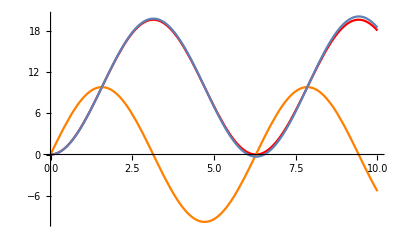

```mathematica
Show[plotExactX,plotExactV, plotApprX, PlotRange -> All] (*i plotApprV? *)
```

## 2 задача. Поведението на топче, закачено на пружина може да бъде моделирано чрез задачата от втори ред: x''(t)=9.8-x, 0<t≤10, x(0) = 0 //началното положение е 0 x'(0) = 0 //началната скорост, с която е пуснато тялото е 0.

```mathematica
F[t_,u_]:={u[[2]], 9.8-u[[1]]} (*u = {x,v}*)
appr = explicitEuler[F,0.01,0,10,{0,0}];
Animate[Graphics[{Circle[{5,appr[[i,2,1]]},1],Line[{{5,appr[[i,2,1]]+1},{5,30}}]}, Axes -> True, PlotRange->{{0,10},{0,30}}],{i,1,Length[appr],1}]
```

## 3 задача. Профилът на капка, висяща от капиляр, може да се опише чрез система от диференциални уравнения dr/ds = cos α dz/ds = sin α dα/ds = 2b+cz -sin α/r r(0)=z(0)=α(0)=0, където s e дължината на дъгата от върха на капката, (r,z) са цилиндрични кординати, α е ъгълът, който сключва допирателната с абсцисната ос и b и c са параметри, които зависи профила -Image- Начертайте профила на капката при b=1 / 0.5424, c=-2.9.

```mathematica
AB4[f_, h_, t0_, T_, u0_] := (
  n = Ceiling[(T - t0)/h];
  x = Table[t0 + i h, {i, 0, n}];
  y = Table[0, {n + 1}];
  fi = Table[0, {n + 1}]; (*list of values of the right-hand side f*)

  y[[1]] = u0;
 fi[[1]]= f[x[[1]], y[[1]]];
 
  (*Compute the first approximate values, using the RK4 method*)
  For[i = 1, i ≤ 3, i++,
   k1 = h f[x[[i]], y[[i]]];
   k2 = h f[x[[i]] + h/2, y[[i]] + k1/2];
   k3 = h f[x[[i]] + h/2, y[[i]] + k2/2];
   k4 = h f[x[[i]] + h, y[[i]] + k3];
   y[[i + 1]] = y[[i]] + 1/6 (k1 + 2 k2 + 2 k3 + k4);
   fi[[i + 1]] = f[x[[i + 1]], y[[i + 1]]];
   ];
   
  (*Compute the remaining values, using the AB4 formula*)
  For[i = 4, i < n + 1, i++,
   y[[i + 1]] = y[[i]] + h /24 (55 fi[[i]] - 59 fi[[i - 1]] + 37 fi[[i - 2]] -9 fi[[i - 3]]);
   fi[[i + 1]] = f[x[[i + 1]], y[[i + 1]]];
   ];
  Transpose[{x, y}]
  )
```

```mathematica
b=1/0.5424;
c=-2.9;
```

```mathematica
(* u = {r,z,a} *)
F[s_, u_] := {Cos[u[[3]]],Sin[u[[3]]],If[s==0,b,2*b+c*u[[2]]-Sin[u[[3]]]/u[[1]]]};
```

```mathematica
appr = AB4[F,0.01,0,10,{0,0,0}];
```

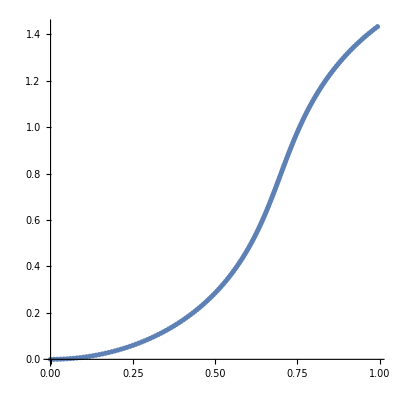

```mathematica
ListPlot[Select[appr[[All,2,1 ;; 2]], #[[1]] ≤ 1 &], AspectRatio->1]
```

## 4 задача. Решете задачата u'(t)=10^6(-u+sin t ), 0<t≤10, u(0) = 0, използвайки явен и неявен метод на Ойлер, Рунге-Кута и Адамс-Башфорт. Сравнете получените решения с точното решение на задачата.

```mathematica
F4[t_,u_] := 10^6(-u+Sin[t])
Clear[exact];
```

```mathematica
exact[t_] = DSolveValue[{u'[t] == 10^6(-u[t]+Sin[t]),u[0]==0},u[t],t];
```

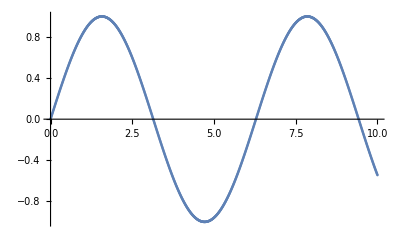

```mathematica
ListPlot[implicitEuler[F4,0.01,0,10,0]]
```

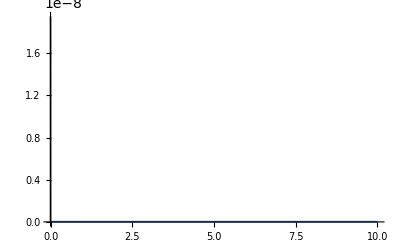

```mathematica
Plot[exact[t],{t,0,10}]
```

## 5 задача. Решете задачата u''-11u'-10u=0, 0<t<=2 u(0)=1 u'(0)=-1 използвайки явен и неявен метод на Ойлер, Рунге-Кута и Адамс-Башфорт. Сравнете получените решения с точното решение на задачата.